```mathematica
Quantum Anharmonic Oscillator
```

Note: you will only need to modify the cells that are light blue. Other cells are used to test your code or demonstrate a couple strategies along the way. 
Note: the guide below is only one possible solution. You are totally welcome to solve the problem in other ways too!

## Introduction to the problem

In this tutorial, we will numerically find the first few energy levels and the corresponding wavefunctions for an anharmonic oscillator. 
For convenience, we will set some constants to 1 and consider the Hamiltonian of the harmonic oscillator to be H=1/2 ℙ^2+1/2 𝕏^2, where ℙ and 𝕏 are the well known momentum and position operators. In terms of the annihilation and creation operators, they are 
ℙ=I(a^†-a)/(√2) and 𝕏=(a^†+a)/(√2) 
The anharmonic oscillator we are going to solve has the following Hamiltonian:
 H=1/2 ℙ^2+1/2 𝕏^4 
 We are going to use the Rayleigh-Ritz Method: We are going to write the Hamiltonian as a truncated sparse matrix in the basis of the harmonic oscillator 
  a^†|n⟩=√(n+1)|n+1⟩
  a^|n⟩=√n|n-1⟩
  and diagonalize it.  
 The wavefunctions of the harmonic oscillator is given by 
 ψ_n(x)=(e^(-x^2/2))/(√(2^n n!√π))H_n(x)
 where H_n(x) are the Hermite functions.

## Chapter One Teaching Mathematica quantum mechanics: ladder operators

## Teach Mathematica about Ladder Operators using several replacements rules

### Understanding patterns in Mathematica: one underscore, two underscores, and three underscores.

As we all know, one underscore will match one object of the specified pattern, understand the following code and its output.

```mathematica
f[]+f[a]+f[a,b]+f[c]+g[a]/.{f[a_]->0}
```

f[]+f[a,b]+g[a]

Two underscores will match one or more objects, understand the following code and its output.

```mathematica
f[]+f[a]+f[a,b]+f[c]+g[a]/.{f[a__]->0}
```

f[]+g[a]

Today we are going to use the pattern with three underscores, which will match any number of objects including zero, understand the following code and its output.

```mathematica
f[]+f[a]+f[a,b]+f[c]+g[a]/.{f[a___]->0}
```

g[a]

### How to multiply operators

The ladder operators are non - commutative. In this exercise we will use the centerdot · (input by using Esc . Esc) to represent operator multiplication. Note centerdot is a pure symbol, mathematica internally does not give it any properties.

#### Why do we need to do this

As centerdot is just a display,  Mathematica is not able to evaluate the expression as it is.

```mathematica
Expand[(2 a +SuperDagger[a])· (a-I SuperDagger[a])]
```

(2 a+a^†)·(a-ⅈ a^†)

If using normal multiplication, Mathematica is not able to realize the operators do not commute.

```mathematica
Expand[(2 a +SuperDagger[a])(a-I SuperDagger[a])]
```

2 a^2+(1-2 ⅈ) a a^†-ⅈ (a^†)^2

#### The rules

This part of the code will teach Mathematica how to evaluate an operator expression according to the distribution rule of operator multiplication while maintaining the order of the operators. (Interested readers could also realize the commutator relationship to make it normal ordered, but we would not need it.)

#### Building your rules step by step

First we will build the distribution rule which includes the left distribution rule and the right distribution rule. In the following, x y and z are arbitrary expressions that are made of numbers and operators. In our current problem, we don’t have to worry about distributing to more than two expressions(but our rules can handle it automatically).
x·(y+z)=x·y+x·z
(x+y)·z=x·z+y·z
but we can combine both rules to get
x·(y+z)·w=x·y·w+x·z·w
Note that either x or w could be zero argument, one argument or more than one arguments.

```mathematica
(*implement your distribution rule here and use the following cells to test your rule*)
distributerule=x___·(y_+z_)·w___-> x·y·w+x·z·w
```

x___·(y_+z_)·w___→x·y·w+x·z·w

```mathematica
(2a+SuperDagger[a])·(I a-SuperDagger[a])//.distributerule//Expand
```

(2 a)·(ⅈ a)+(2 a)·-a^†+a^†·(ⅈ a)+a^†·-a^†

desired output
(2 a)·(ⅈ a)+(2 a)·-a^†+a^†·(ⅈ a)+a^†·-a^†

```mathematica
(2a+SuperDagger[a])·(I a-SuperDagger[a])·(a+SuperDagger[a])//.distributerule//Expand
```

(2 a)·(ⅈ a)·a+(2 a)·(ⅈ a)·a^†+(2 a)·-a^†·a+(2 a)·-a^†·a^†+a^†·(ⅈ a)·a+a^†·(ⅈ a)·a^†+a^†·-a^†·a+a^†·-a^†·a^†

desired output 
(2 a)·(ⅈ a)·a+(2 a)·(ⅈ a)·a^†+(2 a)·-a^†·a+(2 a)·-a^†·a^†+a^†·(ⅈ a)·a+a^†·(ⅈ a)·a^†+a^†·-a^†·a+a^†·-a^†·a^†

Next we will build the linearity rule: 
You can use the build in function NumericQ to test if something is a number

```mathematica
NumericQ[2]
```

True

Understand the following application of replacement rule and its output.

```mathematica
{1,3,2,avariable,6,Pi}/.a_?PrimeQ->a"is prime"
```

{1,3 is prime,2 is prime,avariable,6,π}

```mathematica
(*implement your linearrule here and use the following cell to test your linear rule, think about pattern matching! The implementation is very similar to the distribution law you just implemented.*)
linearrule=c___·(a_?NumericQ d___)·b___->a c·d·b
rules={distributerule,linearrule};
```

c___·(d___ a_?NumericQ)·b___→a c·d·b

```mathematica
(2a+SuperDagger[a])·(I a-SuperDagger[a])//.rules
```

2 ⅈ a·a-2 a·a^†+ⅈ a^†·a-a^†·a^†

desired output
2 ⅈ a·a-2 a·a^†+ⅈ a^†·a-a^†·a^†

```mathematica
(*run this cell: this is the definition of momentum and position operator*)
ℙ=(ⅈ(SuperDagger[a]-a))/(√2);
𝕏=(SuperDagger[a]+a)/(√2);
```

```mathematica
(*this part calculate the harmonic oscillator's Hamiltonian. You don't have to write new code but please run this cell to test that you get the desired output*)

1/2(ℙ·ℙ+𝕏·𝕏)//.rules//Expand
```

(a·a^†)/2+(a^†·a)/2

desired output
(a·a^†)/2+(a^†·a)/2

### How to act operator on eigenstates

The following is how ladder operator on the states. 

  a^†·|n⟩=√(n+1)|n+1⟩
 a ·^|n⟩=√n|n-1⟩
 As we are going to build a matrix, and the matrix in Mathematica counts from 1 and our ground states count from 0. We need to modify the rules above slightly so that in our code ground state is actually |1⟩:
  a^†·|n⟩=√(n+0)|n+1⟩
 a ·^|n⟩=√(n-1)|n-1⟩
 Imply the above rules on the states.

```mathematica
(*implement the above rules on the states( use EscdgEsc to get dagger. use Ket[n] to represent |n⟩), think about pattern matching!*)
creationrule=b___·SuperDagger[a]·Ket[n_]->√n b·Ket[n+1]
annihilationrule=b___·a· Ket[n_]->√(n-1)b·Ket[n-1]
```

b___·a^†·n_→√n b·1+n

b___·a·n_→√(-1+n) b·-1+n

Apply  your rules for harmonic oscillator

```mathematica
(*test that your rules work for harmonic oscillator*)
newrules={rules,creationrule,annihilationrule}//Flatten;
(1/2 ℙ·ℙ·n+1/2 𝕏·𝕏·n)//.newrules//Simplify
```

1/2 (-1+2 n) CenterDot[n]

Desired output

1/2 (-1+2 n) CenterDot[n]

should give (the minus sign is because we defined the ground state to be |1⟩ for convenience to go to matrix later.

The extra CenterDot is annoying, add another rule to get rid of it.

```mathematica
(*implement your rule to get rid of the extra centerdot here*)
unirule=a___·b___->a b
```

a___·b___→a b

```mathematica
(*Check that your rules work for harmonic oscillor*)
finalrules={newrules,unirule}//Flatten;
(1/2 ℙ·ℙ·n+1/2 𝕏·𝕏·n)//.finalrules//Simplify
```

1/2 (-1+2 n) n

Desired output

1/2 (-1+2 n) n

## Chapter Two Solve the anharmonic oscillator problem: eigenvalues and eigenstates

## Your Hamiltonian Matrix

Now act the Hamiltonian of an anharmonic oscillator on the states

```mathematica
(*run this cell. This finds the anharmonic oscillator Hamiltonian in terms of a and a^† and then act on the state n*)
hamiltonian=(1/2 ℙ·ℙ·Ket[n]+1/2 𝕏·𝕏·𝕏·𝕏·Ket[n])//.finalrules
```

(ⅈ (-(ⅈ (-√(-2+n) √(-1+n) -2+n+n n))/(√2)+(ⅈ (-(-1+n) n+√n √(1+n) 2+n))/(√2)))/(2 √2)+1/(2 √2)(1/(√2)(((√(-4+n) √(-3+n) √(-2+n) √(-1+n) -4+n+√(-2+n) √(-1+n) n -2+n)/(√2)+(√(-2+n) (-1+n)^(3/2) -2+n+n (1+n) n)/(√2))/(√2)+(((-2+n)^(3/2) √(-1+n) -2+n+n^2 n)/(√2)+((-1+n) n n+√n √(1+n) (2+n) 2+n)/(√2))/(√2))+1/(√2)((((-3+n) √(-2+n) √(-1+n) -2+n+(-1+n) n n)/(√2)+((-1+n)^2 n+√n (1+n)^(3/2) 2+n)/(√2))/(√2)+(((-2+n) (-1+n) n+n^(3/2) √(1+n) 2+n)/(√2)+((-1+n) √n √(1+n) 2+n+√n √(1+n) √(2+n) √(3+n) 4+n)/(√2))/(√2)))

This is a bit messy. Write a code such that they are organized in terms of the states. 
One way to do this is to use function Collect.

### An example of Collect

First argument is an expression, second argument is a pattern, collect organize the expression in terms of power of the pattern, which is like writing the expression in terms of a series of pattern to certain power.

```mathematica
Collect[x+x^2 Cos[y]^2+a x+x^2 Sin[y]^2,x]
```

(1+a) x+x^2 (Cos[y]^2+Sin[y]^2)

we can then simplify the coefficient by using the third argument, which is a function that is applied to the coefficients

```mathematica
Collect[x+x^2 Cos[y]^2+a x+x^2 Sin[y]^2,x,Simplify]
```

(1+a) x+x^2

This is different from simplify, as demonstrated below.

```mathematica
x+x^2 Cos[y]^2+a x+x^2 Sin[y]^2//Simplify
```

x (1+a+x)

### Your code to organize the Hamiltonian in terms of the states

```mathematica
(*Insert your code here so they are organized in terms of the states*)
organizedH=Collect[hamiltonian,Ket[n___],Simplify]
```

1/8 √(-4+n) √(-3+n) √(-2+n) √(-1+n) -4+n+1/2 (-2+n)^(3/2) √(-1+n) -2+n+1/8 (1-2 n+6 n^2) n+1/2 n^(3/2) √(1+n) 2+n+1/8 √n √(1+n) √(2+n) √(3+n) 4+n

As you can see from above results, only a small fraction of the entries are non zero, which indicates we want to use SparseArray. Thus we need a set of rules for the SparseArray.

### Here is an example of SparseArray, that makes a 5 by 5 matrix while all diagonal term specified and one other entry specified.

```mathematica
SparseArray[{{1,2}->5,{i_,i_}->i},{5,5}]//MatrixForm
```

(1 | 5 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 4 | 0
0 | 0 | 0 | 0 | 5)

### In the following you will make your own rules with Cases for the SparseArray and then make your own SparseArray for the Hamiltonian

#### An example of Cases

Use Cases to achieve this: Cases[expression, pattern->do something with the particular pattern], check out the following example that picks out the list that has two elements

```mathematica
Cases[{{1,2},{2},{3,4,1},{5,4},{3,3}},{a_,b_}]
```

{{1,2},{5,4},{3,3}}

In this example, the output is replaced by the sum of the two elements

```mathematica
Cases[{{1,2},{2},{3,4,1},{5,4},{3,3}},{a_,b_}->a+b]
```

{3,9,6}

#### Make your Hamiltonian matrix:

Your desired output should be replacement rules of this form {n_, m_} /; m == n - 4 -> coefficient of | n - 4⟩

```mathematica
(*Implement your rules to make the rules for the sparsearray here using cases on the organizedH*)
matrixrules=Cases[organizedH,c_ Ket[l_]-> {n_,m_}/;m==l->c]/.{n$-> n,m$->m}
```

{{n_,m_}/;m==-4+n→1/8 √(-4+n) √(-3+n) √(-2+n) √(-1+n),{n_,m_}/;m==-2+n→1/2 (-2+n)^(3/2) √(-1+n),{n_,m_}/;m==n→1/8 (1-2 n+6 n^2),{n_,m_}/;m==2+n→1/2 n^(3/2) √(1+n),{n_,m_}/;m==4+n→1/8 √n √(1+n) √(2+n) √(3+n)}

```mathematica
(*Insert your matrix rules and make a large (100 by 100)(matrix and view with ArrayPlot*)
size=100;
yourmatrix=SparseArray[matrixrules,{size,size}]
yourmatrix//ArrayPlot
```

SparseArray[…]

-Graphics-

## Energies and Wavefunctions

First we need to convert our matrix into numbers otherwise Mathematica will try to diagonalize the matrix analytically.

```mathematica
(*Run this cell, it turns your matrix into numbers*)
yourmatrixN=N[yourmatrix,30];
```

Now extract the last 6 eigenvalues (Mathematica organizes her eigenvalues to go from largest to smallest) and multiply by 2 and compare with the following result obtained by WKB approximation. (The literature (hep-th/9812211 and ref within)studies a Hamiltonian given by p^2+x^4, thus our result is off by 2.) Use help to learn about the scope of function Eigensystem.

```mathematica
(*Extract last six eigenvalues of yourmatrixN and multiply by 2 to compare with the literature*)
energies=Take[Eigenvalues[yourmatrixN],-6]2
```

{21.2383729182359406799176606835,16.2618260188502260203075989379,11.6447455113781620227839770483,7.45569793798673839306615267346,3.79967302980139416879714485429,1.06036209048418289964949748957}

In order to draw the wavefunctions, we need the eigenvectors too, and make use of the set of given wavefunctions of harmonic oscillator given before, (again, n-1 due to ground state is |1⟩)

```mathematica
(*Run this cell. It implements all the wavefunctions for the harmonic oscillator.*)
ψ[n_, x_]:=(ⅇ^(-x^2/2))/(√(2^(n-1)(n-1)!√π))HermiteH[n-1,x];
listofwavefunction=Table[ψ[i, x],{i,1,size}];
```

Now build the six new wavefunctions for the anharmonic oscillator and shifted by the eigenvalues so we can view all of them on the same plot together with the potential. Try to use Matrix multiplication to get all the new wavefunctions at once.

```mathematica
eigenguys=Eigenvectors[yourmatrixN,-6].listofwavefunction
```

{1,1,1,1,1,0.74509847120107221522589009082 ⅇ^(-x^2/2)+150+5.4383286067668251619250377004×10^-137 ⅇ^(-x^2/2) (1)}
 |  |  |  |

```mathematica
Length[eigenguys]
```

6

```mathematica
(*Insert your new wavefunctions (shifted by the eigenvalues) here*)
newwavefuns=Eigenvectors[yourmatrixN,-6].listofwavefunction
```

{1,1,1,1,1,0.74509847120107221522589009082 ⅇ^(-x^2/2)+150+5.4383286067668251619250377004×10^-137 ⅇ^(-x^2/2) (1)}
 |  |  |  |

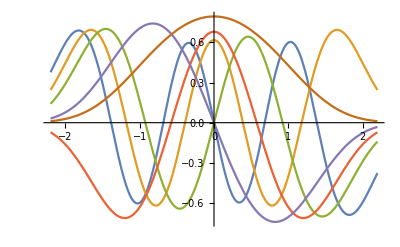

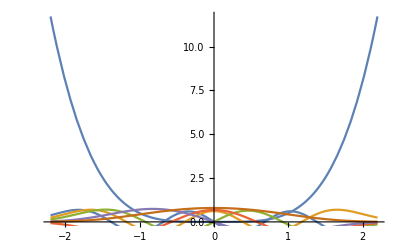

```mathematica
(*Display the plots of your new wavefunctions together with the potential, the range of x is chosen for viewing convenience.*)
plot1=Plot[x^4/2,{x,-2.2,2.2}];
plot2=Plot[newwavefuns,{x,-2.2,2.2}]
Show[plot1,plot2]
```

## Random question: What would you call the person who works with phones from Zagreb.

The croatian operator. (credit: Juan Cayuso)